```mathematica
DiffurStruc[func_,arg_,cprFunc_,ccur_]:={func'[arg]-ccur-cprFunc[func[arg]]==0};
DiffurIni[func_,InitialPoint_,InitialValue_]:={func[InitialPoint]==InitialValue};
Diffur[func_,arg_,cprFunc_,ccur_,InitialPoint_,InitialValue_]:=Flatten[
{DiffurStruc[func,arg,cprFunc,ccur],DiffurIni[func,InitialPoint,InitialValue]}];
```

```mathematica
CommonCPR[ccur_, cprFunc_, InitialPoint_,InitialValue_, {arg_,lowRange_,upperRange_}]:=
NDSolve[Diffur[γ,arg,cprFunc,ccur,InitialPoint,InitialValue],γ[arg],{arg,lowRange,upperRange}];
UsualRSJ[ccur_,InitialPoint_,InitialValue_]:=
Diffur[γ,t,(Sin[#]+0.4Sin[2#])&,ccur,InitialPoint,InitialValue];
SolveRSJ[ccur_,InitialPoint_,InitialValue_,range_]:=
NDSolve[
UsualRSJ[ccur,InitialPoint,InitialValue],
γ[t],
Flatten[{t,range}]];
PlotRSJSolution[ccur_,InitialPoint_,InitialValue_,range_]:=
Plot[
Evaluate[γ[t]/.SolveRSJ[ccur,InitialPoint,InitialValue,range]],
Flatten[{t,range}]
];
PlotRSJDSolution[ccur_,InitialPoint_,InitialValue_,range_]:=
Plot[
Evaluate[γ'[t]/.D[SolveRSJ[ccur,InitialPoint,InitialValue,range],t]],
Flatten[{t,range}]
];
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
averDiffer[list_]:=Module[{l},
l={};
For[i=1,i≤Length[list]-1,i++,AppendTo[l,list[[i+1]]-list[[i]]]];
Mean[l]];
periodGet[func_,{arg_,ini_,fin_}]:=averDiffer[findAllRoots[func,{arg,ini,fin}]];
```

```mathematica
sol[ccur_]:=Flatten@SolveRSJ[ccur,0,0,{-4π,6π}];
γ[t]/.sol[1.1]
```

```mathematica
InterpolatingFunction[…][t]
```

InterpolatingFunction[…][t]

```mathematica
plots[ccur_]:=Plot[Evaluate[{γ[t]/.sol[ccur],γ'[t]/.D[sol[ccur], t],γ''[t]/.D[D[sol[ccur], t], t]}],{t,-4π,6π}];
plots[1.4]
```

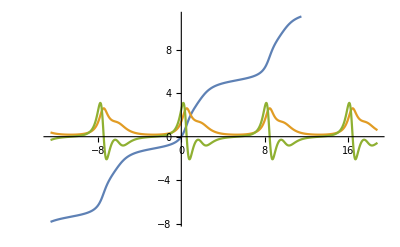

-Graphics-

```mathematica
periodGet[Evaluate[γ''[t]/.D[D[sol[1], t], t]]]
```

ReplaceAll::reps: {0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

periodGet[γ''[t]/.0]

```mathematica
long=Table[{π/periodGet[Evaluate[γ''[t]/.D[D[sol[n], t], t]],{t,-4π,6π}],n},{n,1.1,10,0.1}]
```

ReplaceAll::reps: {0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{π/Mean[{}],1.1},{π/Mean[{}],1.2},{π/Mean[{}],1.3},{π/Mean[{}],1.4},{π/Mean[{}],1.5},{π/Mean[{}],1.6},{π/Mean[{}],1.7},{π/Mean[{}],1.8},{π/Mean[{}],1.9},{π/Mean[{}],2.},{π/Mean[{}],2.1},{π/Mean[{}],2.2},{π/Mean[{}],2.3},{π/Mean[{}],2.4},{π/Mean[{}],2.5},{π/Mean[{}],2.6},{π/Mean[{}],2.7},{π/Mean[{}],2.8},{π/Mean[{}],2.9},{π/Mean[{}],3.},{π/Mean[{}],3.1},{π/Mean[{}],3.2},{π/Mean[{}],3.3},{π/Mean[{}],3.4},{π/Mean[{}],3.5},{π/Mean[{}],3.6},{π/Mean[{}],3.7},{π/Mean[{}],3.8},{π/Mean[{}],3.9},{π/Mean[{}],4.},{π/Mean[{}],4.1},{π/Mean[{}],4.2},{π/Mean[{}],4.3},{π/Mean[{}],4.4},{π/Mean[{}],4.5},{π/Mean[{}],4.6},{π/Mean[{}],4.7},{π/Mean[{}],4.8},{π/Mean[{}],4.9},{π/Mean[{}],5.},{π/Mean[{}],5.1},{π/Mean[{}],5.2},{π/Mean[{}],5.3},{π/Mean[{}],5.4},{π/Mean[{}],5.5},{π/Mean[{}],5.6},{π/Mean[{}],5.7},{π/Mean[{}],5.8},{π/Mean[{}],5.9},{π/Mean[{}],6.},{π/Mean[{}],6.1},{π/Mean[{}],6.2},{π/Mean[{}],6.3},{π/Mean[{}],6.4},{π/Mean[{}],6.5},{π/Mean[{}],6.6},{π/Mean[{}],6.7},{π/Mean[{}],6.8},{π/Mean[{}],6.9},{π/Mean[{}],7.},{π/Mean[{}],7.1},{π/Mean[{}],7.2},{π/Mean[{}],7.3},{π/Mean[{}],7.4},{π/Mean[{}],7.5},{π/Mean[{}],7.6},{π/Mean[{}],7.7},{π/Mean[{}],7.8},{π/Mean[{}],7.9},{π/Mean[{}],8.},{π/Mean[{}],8.1},{π/Mean[{}],8.2},{π/Mean[{}],8.3},{π/Mean[{}],8.4},{π/Mean[{}],8.5},{π/Mean[{}],8.6},{π/Mean[{}],8.7},{π/Mean[{}],8.8},{π/Mean[{}],8.9},{π/Mean[{}],9.},{π/Mean[{}],9.1},{π/Mean[{}],9.2},{π/Mean[{}],9.3},{π/Mean[{}],9.4},{π/Mean[{}],9.5},{π/Mean[{}],9.6},{π/Mean[{}],9.7},{π/Mean[{}],9.8},{π/Mean[{}],9.9},{π/Mean[{}],10.}}

```mathematica
Plot[x,{x,0,10},Epilog->{PointSize[Medium],Map[Point[#]&,long]}]
```

```mathematica
solution[ccur_, cprFunc_]:=Flatten[γ[t]/.CommonCPR[ccur, cprFunc,0,0,{t,0,1000π}]];
```

```mathematica
(solution[1.2,Sin]/.t->1000π)/(1000π)
```

{0.663544}

```mathematica
Clear[i];
Manipulate[Plot[{(solution[i,(Sin[#]+a Sin[2#]+b Sin[3#])&]/.t->1000π)/(1000π),i},{i,0,10}],{a,0,1},{b,0,1}]
```